## Введение: примеры для метода Галеркина (без МКЭ)

### Пример 1: простейший пример использования метода Галеркина

Рассмотрим дифференциальное уранение Au=f, невязка уравнения R=Au-f
Ищем решение в виде u=∑_(i=1)^n c_i ϕ_i, ϕ_i - базисная функция,
Метод Галеркина заключается в ортогонализации невязки: (R,ψ_j)=0,j=1..n, ψ_j- проекционная функция
(1) Частный случай ψ_j=ϕ_j - метод Бубнова-Галеркина
(2) Частный случай ψ_j!=ϕ_j - метод Галеркина-Петрова

u''=x^2,u(0)=u(1)=0,оператор A=d^2/dx^2

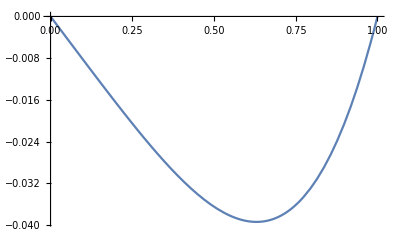

```mathematica
f[x_]:=x^2
ul=0;
ur=0;
sol=NDSolveValue[{y''[x]==f[x],y[0]==ul,y[1]==ur},y[x],x];
Plot[sol,{x,0,1}]
```

В качестве базисных функций возьмем две функции ϕ_1=sin(πx)и ϕ_2=sin(2πx). Сразу отметим, что они удовлетворяют граничным условиям.

```mathematica
u[x_]:=c1 Sin[π x]+c2 Sin[2 π x]
```

Запишем невязку:

```mathematica
r[x_]:=D[u[x],x,x]-f[x]
```

Составим систему из двух уравнений  (R,ϕ_1)=0  и (R,ϕ_2)=0:

```mathematica
eq1=Integrate[r[x]*Sin[π x],{x,0,1}];
eq2=Integrate[r[x]*Sin[2π x],{x,0,1}];
csol=Solve[{eq1==0,eq2==0}][[1]]
```

{c1→-(2 (-4+π^2))/π^5,c2→1/(4 π^3)}

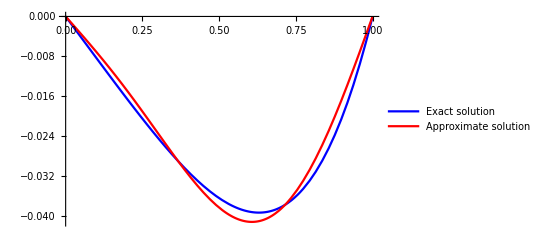

```mathematica
Plot[{sol,u[x]/.csol},{x,0,1},PlotStyle->{Blue,Red},PlotLegends->{"Exact solution","Approximate solution"}]
```

### Пример 2: более сложное уравнение и больше базисных функций

u''-5u'-u=Exp[x],u(0)=u(1)=0,оператор A=d^2/dx^2-5 d/dx-id

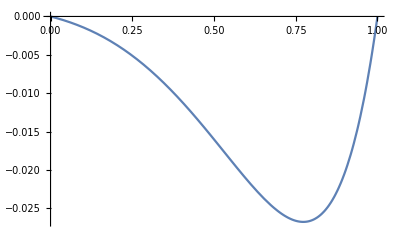

```mathematica
f[x_]:=x^2
op[f_]:=D[f,x,x]-5D[f,x]-f
ul=0;
ur=0;
sol=NDSolveValue[{op[y[x]]==f[x],y[0]==ul,y[1]==ur},y[x],x];
Plot[sol,{x,0,1}]
```

В качестве базисных функций возьмем функции ϕ_j=sin(jπx),они удовлетворяют граничным условиям.
 Система (R,ϕ_j)=(Au-f,ϕ_j)=(∑_(i=1)^n c_i Aϕ_i-f,ϕ_j)=0.
Матрица системы  M_ij=(Aϕ_i,ϕ_j),правая часть F_j=(f,ϕ_j).

```mathematica
n=8;
M=ParallelTable[Integrate[op[Sin[i π x]]*Sin[j π x],{x,0,1}],{j,n},{i,n}]//N;
```

Матрица M, в общем случае, является плотно заполненной :

```mathematica
MatrixForm@M
```

(-5.4348 | 6.66667 | 0. | 2.66667 | 0. | 1.71429 | 0. | 1.26984
-6.66667 | -20.2392 | 12. | 0. | 4.7619 | 0. | 3.11111 | 0.
0. | -12. | -44.9132 | 17.1429 | 0. | 6.66667 | 0. | 4.36364
-2.66667 | 0. | -17.1429 | -79.4568 | 22.2222 | 0. | 8.48485 | 0.
0. | -4.7619 | 0. | -22.2222 | -123.87 | 27.2727 | 0. | 10.2564
-1.71429 | 0. | -6.66667 | 0. | -27.2727 | -178.153 | 32.3077 | 0.
0. | -3.11111 | 0. | -8.48485 | 0. | -32.3077 | -242.305 | 37.3333
-1.26984 | 0. | -4.36364 | 0. | -10.2564 | 0. | -37.3333 | -316.327)

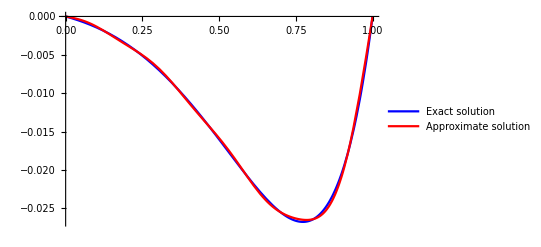

```mathematica
F=ParallelTable[Integrate[f[x]*Sin[j π x],{x,0,1}],{j,n}]//N;
csol=LinearSolve[M,F];
u[x_]:=Evaluate@Total@Table[csol[[i]]Sin[i π x],{i,n}]
Plot[{sol,u[x]},{x,0,1},PlotStyle->{Blue,Red},PlotLegends->{"Exact solution","Approximate solution"}]
```

Замечание: случай с граничными условиями общего вида au+bu’=c здесь не рассматриваем, он будет разобран далее в методе конечных элементов.

## МКЭ 1d

### Пример 3: простейшая реализация МКЭ для уравнения u”=f

u''=x^2,u(0)=ul,u(1)=ur

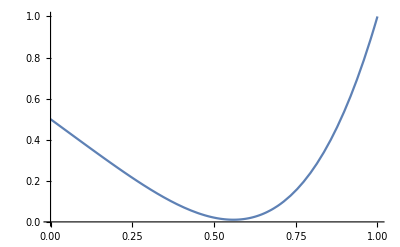

```mathematica
f[x_]:=20 x^2
op[f_]:=D[f,x,x]
ul=0.5;
ur=1;
sol=NDSolveValue[{op[y[x]]==f[x],y[0]==ul,y[1]==ur},y[x],x];
pl=Plot[sol,{x,0,1}]
```

Введем сетку узлов x_1..x_n. В качестве базисных функций возьмем ϕ_i(x)={(x-x_(i-1))/(x_i-x_(i-1)),x∈[x_(i-1);x_i], (x-x_(i+1))/(x_i-x_(i+1)), x∈[x_i;x_(i+1)], 0 при x!∈[x_(i-1);x_(i+1)]} - функции “домики”.
Функции  ϕ_1(x) и  ϕ_n(x) возьмем “половинчатые”: ϕ_1(x)={(x-x_2)/(x_2-x_1),x∈[x_1;x_2], 0 при x!∈[x_1;x_2]}, ϕ_n(x)={(x-x_n)/(x_(n-1)-x_n),x∈[x_(n-1);x_n],  0 при x!∈[x_(n-1);x_n]}.

Функции ϕ_i(x) и пример функций для сетки из трех узлов:

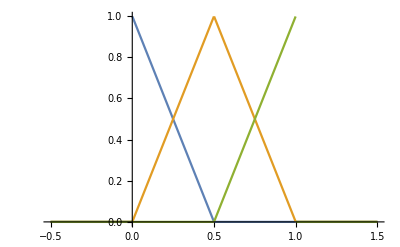

```mathematica
ϕ[x1_,x2_,x3_,x_]:=Piecewise[{{(x-x1)/(x2-x1),x1<=x<=x2},{(x-x3)/(x2-x3),x2<=x<=x3}},0]
ϕleft[x1_,x2_,x_]:=Piecewise[{{(x-x2)/(x1-x2),x1<=x<=x2}},0]
ϕright[x2_,x3_,x_]:=Piecewise[{{(x-x2)/(x3-x2),x2<=x<=x3}},0]
Plot[{ϕleft[0,0.5,x],ϕ[0.,0.5,1,x],ϕright[0.5,1,x]},{x,-0.5,1.5},PlotRange->All]
```

Рассмотрим уравнение
u''=f,
α_l u+β_l u'=γ_l при x=0,
α_r u+β_r u'=γ_r при x=1.
Запишем (R,v)=(u''-f,v)=∫_0^1 u''vⅆx-∫_0^1 fvⅆx=//Используем формулу (u'v)'=u''v+u'v'//=
=∫_0^1 (u'v)'ⅆx-∫_0^1 u'v'ⅆx-∫_0^1 fvⅆx=(u'v)|_0^1-∫_0^1 u'v'ⅆx-∫_0^1 fvⅆx=((γ_r/β_r-α_r/β_r u)v)_(x=1)-((γ_l/β_l-α_l/β_l u)v)_(x=0)-∫_0^1 u'v'ⅆx-∫_0^1 fvⅆx=0.
Далее используем, что v=ψ_j=ϕ_j (метод Бубнова-Галеркина), а вместо u подставляем разложение 
u=∑_(i=1)^n c_i ϕ_i. В точках x=0 и x=1 имеют ненулевое значение только ϕ_1 и ϕ_n соответственно, получаем:
((γ_l/β_l-α_l/β_l u)v)_(x=0)=(γ_l/β_l-α_l/β_l с_1 ϕ_1(0))ϕ_1(0)=γ_l/β_l-α_l/β_l с_1;
((γ_r/β_r-α_r/β_r u)v)_(x=1)=(γ_r/β_r-α_r/β_r с_n ϕ_1(0))ϕ_1(0)=γ_r/β_r-α_r/β_r с_n;
Получим в итоге -(γ_r/β_r-α_r/β_r с_n)+γ_l/β_l-α_l/β_l с_1+∫_0^1 u'v'ⅆx=∫_0^1 fvⅆx.
Матрица системы M_ij (аналогично матрице из 2 -го примера)примет вид M_ij=(ϕ_i',ϕ_j'),а правая часть  F_j=-(f,ϕ_j).

```mathematica
n=5;
```

Разобьем отрезок на n-1 часть, получим n узлов:

```mathematica
points=Subdivide[0,1.,n-1]
```

{0.,0.25,0.5,0.75,1.}

Базисные функции и их графики :

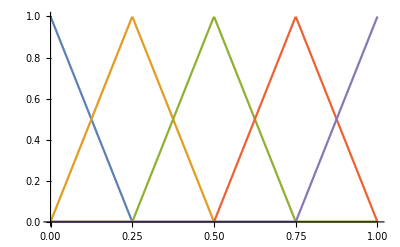

```mathematica
phi={ϕleft[points[[1]],points[[2]],x]}~Join~Table[ϕ[points[[i]],points[[i+1]],points[[i+2]],x],{i,n-2}]~Join~{ϕright[points[[-2]],points[[-1]],x]};
Plot[phi,{x,0,1},PlotRange->All]
```

Как и в примере 2,составим матрицу  M_ij  и вектор правой части F_j:

```mathematica
M=ParallelTable[Integrate[-D[phi[[i]],x]*D[phi[[j]],x],{x,0,1}],{j,n},{i,n}]//N;
```

Заметим, что матрица получилась разреженная, а точнее, трехдиагональная :

```mathematica
MatrixForm@M
```

(-4. | 4. | 0. | 0. | 0.
4. | -8. | 4. | 0. | 0.
0. | 4. | -8. | 4. | 0.
0. | 0. | 4. | -8. | 4.
0. | 0. | 0. | 4. | -4.)

```mathematica
F=ParallelTable[Integrate[f[x]*phi[[j]],{x,0,1}],{j,n}]//N;
```

Левое граничное условие u=ul перепишем в виде u+εu'=ul, где ε - малое число. Тогда γ_l/β_l-α_l/β_l с_1=ul/β_l-1/β_l с_1=m(ul-с_1), m - большое число. В этом случае в матрицу системы M к элементу (1,1) добавится m, а в правую часть F(1)+=m*ul. Число m обычно выбирают порядка 10^(10..20).
Правое граничное условие u=ur перепишем в виде u+εu'=ur, тогда γ_r/β_r-α_r/β_r с_n=ur/β_r-1/β_r с_n=m(ur-с_n). В этом случае в матрицу системы M к элементу (n,n) добавится m, а в правую часть F(n)+=m*ur.
Данный способ учета граничных условий называется методом штрафов.

```mathematica
M[[1,1]]+=10^10;
M[[-1,-1]]+=10^10;
F[[1]]+=10^10 ul;
F[[-1]]+=10^10 ur;
```

Из - за метода штрафов система получается плохо обусловленной:

```mathematica
csol=LinearSolve[M,F];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.×10^10,4.,0.,0.,0.},{4.,-8.,4.,0.,0.},{0.,4.,-8.,4.,0.},{0.,0.,4.,-8.,4.},{0.,0.,0.,4.,1.×10^10}} may contain significant numerical errors.

```mathematica
u=Total@Table[csol[[i]]phi[[i]],{i,n}];
```

Здесь можно наглядно увидеть, что коэффициенты разложения c_i равны значению неизвестной функции в узле x_i (следует из того,что базисная функция ϕ_i равна единице в узле x_i):

```mathematica
nodenum=3;
{u/.x->points[[nodenum]],csol[[nodenum]]}
```

{0.0208333,0.0208333}

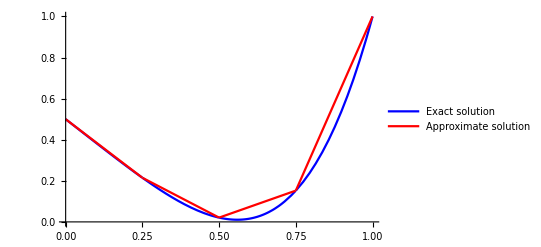

```mathematica
Plot[{sol,u},{x,0,1},PlotStyle->{Blue,Red},PlotLegends->{"Exact solution","Approximate solution"}]
```

### Пример 4: функции формы

```mathematica
f[x_]:=20 x^2
op[f_]:=D[f,x,x]
ul=0.5;
ur=1;
sol=NDSolveValue[{op[y[x]]==f[x],y[0]==ul,y[1]==ur},y[x],x];
pl=Plot[sol,{x,0,1}];
```

Рассмотрим отрезок с узлами i и j (будем называть его элементом), этот отрезок будет иметь номер l (в предыдущем примере было j = i + 1), на нем не равны нулю только базисные функции ϕ_i и ϕ_j, при этом от ϕ_i мы получим участок прямой, который назовем (N^i)_el, а от ϕ_j участок прямой, который назовем (N^j)_el (эти функции не равны нулю только на отрезке l):

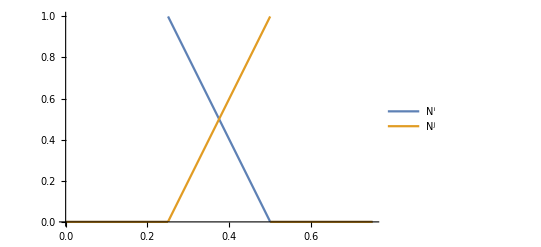

```mathematica
Plot[{ϕleft[0.25,0.5,x],ϕright[0.25,0.5,x]},{x,0,0.75},PlotRange->All,PlotLegends->{"N^i","N^j"}]
```

((Так как u=∑_(i=1)^n c_i ϕ_i=∑_(i=1)^n u_i ϕ_i (так как значение функции в узле x_i равно c_i, логично эти коэффициенты обозначить u_i), то значение функции на элементе l можно записать в виде 
u_l=u_i N_el^i+u_j N_el^j, или в матричном виде u_l=[N^i N^j])_el*{u_i u_j}^T. N^i называется функцией формы, а (матрица [N])_el=[N^i N^j])_el матрицей функций формы элемента.
 Можно записать это же выражение как u_l=[N^i N^j][0 ..0 1 0..               0; 
																		   0 .. .     0    0 1 0..0]*{u_1 u_2 .. u_n}^T=([N]_el[a])_el{u}, ({u} - столбец), [a]_el - матрица геометрических связей размера 2*n,у которой единицы стоят в столбцах i и j. Таким образом,мы перешли от суммирования по узлам к суммированию по элементам:
u=∑_(i=1)^n u_i ϕ_i=∑_(el=1)^n ([N]_el[a])_el{u}.
Проекционную функцию v мы представим в таком же виде: v=∑_(i=1)^n v_i ϕ_i=∑_(el=1)^n (({v}^T[a])_el^T[N])_el^T (так как результат скаляр, его можно без проблем транспонировать).

Ранее мы получили выражение (R,v)=((γ_r/β_r-α_r/β_r u)v)_(x=1)-((γ_l/β_l-α_l/β_l u)v)_(x=0)-∫_0^1 u'v'ⅆx-∫_0^1 fvⅆx=0. Подставим туда наши разложения.
(1)Слагаемое ∫_0^1 fvⅆx=∫_0^1 f∑_(el=1)^n (({v}^T[a])_el^T[N])_el^T ⅆx={v}^T∑_(el=1)^n [a]_el^T∫_Ω_el f[N]_el^T ⅆx, где интегралы в сумме берутся лишь по отрезку el, так как за пределами этого отрезка N_el^i=0.

(2)∫_0^1 u'v'ⅆx=∫_0^1 ∑_(el1=1)^n ({v}^T[a])_el1^T(d/dx[N])_el1^T∑_(el2=1)^n ((d/dx[N])_el2[a])_el2{u}ⅆx=//двойная сумма сводится к одинарной, так как при el1!=el2 произведение функций формы дает ноль - они определены на разных отрезках;по этой же причине интеграл от 0 до 1 берется только по отрезку соответствующего элемента;сумму можно поменять местами с интегралом, а {v}^T и {u} - константы, можно вынести за знак интеграла и суммы//={v}^T(∑_(el=1)^n [a]_el^T((∫_Ω_el (d/dx[N])_el^T(d/dx[N])_el ⅆx)[a])_el){u}. Интеграл ∫_Ω_el (d/dx[N])_el^T(d/dx[N])_el ⅆx=[K]_el - матрица жесткости элемента, ее размер равен 2*2 для линейных функций формы.

(3) В слагаемых, отвечающих за граничные условия, получим, что u(1)=u_n и u(0)=u_1, следовательно, ((γ_r/β_r-α_r/β_r u)v)_(x=1)=∑_(el=1)^n ((({v}^T[a])_el^T[N])_el^T)_(x=1)(γ_r/β_r-α_r/β_r u_n)={v}^T∑_(el=1)^n ([a]_el^T[N])_el^T(x=1)(γ_r/β_r-α_r/β_r u_n); так как в узле n (то  есть при x=1)только функция формы, соответствующая n-му узлу, равна единице, а другие равны нулю,это выражение примет вид  ({v}^T[0..0 1])^T(γ_r/β_r-α_r/β_r u_n).
Аналогично, ((γ_l/β_l-α_l/β_l u)v)_(x=0)=({v}^T[1..0 0])^T(γ_l/β_l-α_l/β_l u_1).

В итоге (R,v)={v}^T([0..0 1]^T(γ_r/β_r-α_r/β_r u_n)-[1..0 0]^T(γ_l/β_l-α_l/β_l u_1)-(∑_(el=1)^n (([a]_el^T[K])_el[a])_el){u}-∑_(el=1)^n [a]_el^T∫_Ω_el f[N]_el^T ⅆx)=0. 
В силу произвольности функции v,коэффициенты v_i произвольны,и написанное выше выражение равно нулю в случае, если все слагаемые равны нулю:  
[0..0 1]^T(γ_r/β_r-α_r/β_r u_n)-[1..0 0]^T(γ_l/β_l-α_l/β_l u_1)-(∑_(el=1)^n (([a]_el^T[K])_el[a])_el){u}-∑_(el=1)^n [a]_el^T∫_Ω_el f[N]_el^T ⅆx=0.
Получили СЛАУ:
-[0..0 1]^T(γ_r/β_r-α_r/β_r u_n)+[1..0 0]^T(γ_l/β_l-α_l/β_l u_1)+(∑_(el=1)^n (([a]_el^T[K])_el[a])_el){u}=-∑_(el=1)^n [a]_el^T∫_Ω_el f[N]_el^T ⅆx.

Так как (матрица [a])_el^T имеет размер n*2, [K]_el - 2*2 (и [a])_el - 2*n, в итоге получаем матрицу n*n - глобальную матрицу жесткости. Элементы локальной матрицы жесткости будут записывать в ячейки i и j глобальной матрицы. Например, для элемента с узлами 2 и 4, если всего 5 узлов, это выглядит так:

```mathematica
a={{0,1,0,0,0},{0,0,0,1,0}};
k={{k11,k12},{k21,k22}};
Print["[a]_el=",MatrixForm@a,", [K]_el=",MatrixForm@k,", прибавляется в глобальную матрицу жесткости:"MatrixForm[Transpose[a].k.a]]
```

[a]_el=(0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0), [K]_el=(k11 | k12
k21 | k22), прибавляется в глобальную матрицу жесткости: (0 | 0 | 0 | 0 | 0
0 | k11 | 0 | k12 | 0
0 | 0 | 0 | 0 | 0
0 | k21 | 0 | k22 | 0
0 | 0 | 0 | 0 | 0)

Для правой части получаем аналогично, но запись идет в вектор, а не матрицу :

```mathematica
a={{0,1,0,0,0},{0,0,0,1,0}};
fn={fn1,fn2};
Print["[a]_el=",MatrixForm@a,", [f]_el=",MatrixForm@fn,", прибавляется в глобальную матрицу жесткости:"MatrixForm[Transpose[a].fn]]
```

[a]_el=(0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0), [f]_el=(fn1
fn2), прибавляется в глобальную матрицу жесткости: (0
fn1
0
fn2
0)

Для граничных условий получаем, что слагаемое α_r/β_r прибавляется в ячейку (n,n) глобальной матрицы жесткости, а  γ_r/β_r прибавляется в n-ю ячейку вектора правой части.
Аналогично α_l/β_l прибавляется в ячейку (1,1)глобальной матрицы жесткости и γ_l/β_l в ячейку (1) вектора правой части.

Перейдем к решению задачи . Зададим функции формы элемента (выражения те же самые, что для ϕleft и ϕright) :

```mathematica
Subscript[N, 1][x1_,x2_,x_]:=Piecewise[{{(x-x2)/(x1-x2),x1<=x<=x2}},0]
Subscript[N, 2][x1_,x2_,x_]:=Piecewise[{{(x-x1)/(x2-x1),x1<=x<=x2}},0]
```

```mathematica
n=5;
nodes=Subdivide[0,1.,n-1]
```

{0.,0.25,0.5,0.75,1.}

Номера узлов :

```mathematica
numnodes=Range[n]
```

{1,2,3,4,5}

Зададим элементы :

```mathematica
elems=Partition[nodes,2,1]
```

{{0.,0.25},{0.25,0.5},{0.5,0.75},{0.75,1.}}

Номера узлов элементов :

```mathematica
elemnumnodes=Partition[numnodes,2,1]
```

{{1,2},{2,3},{3,4},{4,5}}

Функции для вычисления локальной матрицы жесткости и правой части :

```mathematica
Kloc[points_]:=Module[{x1=points[[1]],x2=points[[2]]},Table[Integrate[D[ Subscript[N, i][x1,x2,x],x]D[Subscript[N, j][x1,x2,x],x],{x,x1,x2}],{i,2},{j,2}]]
Floc[points_]:=Module[{x1=points[[1]],x2=points[[2]]},Table[NIntegrate[ -Subscript[N, i][x1,x2,x]f[x],{x,x1,x2}],{i,2}]]
```

Сборка глобальной матрицы жесткости и правой части :

```mathematica
Kglobal=SparseArray[{},{n,n}];
Fglobal=SparseArray[{},{n}];
For[el=1,el<=Length@elems,++el,Kglobal[[elemnumnodes[[el]],elemnumnodes[[el]]]]+=Kloc[elems[[el]]];Fglobal[[elemnumnodes[[el]]]]+=Floc[elems[[el]]]]
```

Граничные условия как в примере 3 :

```mathematica
Kglobal[[1,1]]+=10^10;
Kglobal[[-1,-1]]+=10^10;
Fglobal[[1]]+=10^10 ul;
Fglobal[[-1]]+=10^10 ur;
usol=LinearSolve[Kglobal,Fglobal];
```

Замечание : матрица, правая часть и решение системы получились те же самые, что и в 3 примере! Мы лишь изменили немного способ их получения.

Вычислим значения функции на каждом элементе в 2 точках, по ним потом построим график (так как функции линейные, достаточно взять 2 точки)

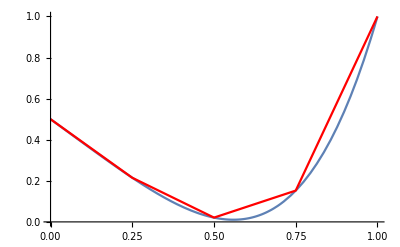

```mathematica
values=DeleteDuplicates@Partition[Flatten[Table[p1=elems[[i,1]];p2=elems[[i,2]];idx1=elemnumnodes[[i,1]];idx2=elemnumnodes[[i,2]];({#,Subscript[N, 1][p1,p2,#]*usol[[idx1]]+Subscript[N, 2][p1,p2,#]*usol[[idx2]]})&/@Subdivide[p1,p2,2],{i,Length@elems}]],2];
Show[pl,ListLinePlot[values,PlotStyle->Red]]
```

### Пример 5: барицентрические координаты и численное интегрирование

```mathematica
Clear["Global`*"]
f[x_]:=20 x^2
op[f_]:=D[f,x,x]
ul=0.5;
ur=1;
sol=NDSolveValue[{op[y[x]]==f[x],y[0]==ul,y[1]==ur},y[x],x];
pl=Plot[sol,{x,0,1}];
```

Рассмотрим интеграл ∫_Ω_el f[N]_el^T ⅆx=∫_a^b f[N]_el^T ⅆx. Проведем замену x=a+ξ (b-a), получим ∫_a^b f((x)[N(x)])_el^T ⅆx=∫_-1^1 f((a+ξ(b-a))[N(a+ξ(b-a))])^T*(b-a)ⅆξ. Якобиан преобразования J=b-a есть длина отрезка.
Посмотрим, какой вид примут функции формы:

```mathematica
{Subscript[N, 1][a,b,a+ξ (b-a)],Subscript[N, 2][a,b,a+ξ (b-a)]}//FullSimplify
```

{Piecewise[{{1-ξ, a≤a-a ξ+b ξ≤b}, {0, True}}],Piecewise[{{ξ, a≤a+(-a+b) ξ≤b}, {0, True}}]}

Таким образом, мы свели интегрирование по произвольному отрезку к интегрированию по отрезку от 0 до 1, где функции формы имеют простой вид . Данный отрезок, а точнее, элемент, называется референсным элементом, а функции формы на нем имеют вид N_1=1-ξ и N_2=ξ, узел с координатой x=0 имеет номер 1, с координатой x=1 - номер 2.
Введем теперь барицентрические координаты на отрезке. Пусть точка S∈[0;1], точка A имеет координату x=0, точка B координату x=1. Тогда L_1=SB/AB, L_2=AS/AB - L-координаты (они же барицентрические координаты) на отрезке. С помощью них можно записать функции формы: N_1=L_1, N_2=L_2. При L_1=0 имеем S=B и N_1=0, N_2=1. При L_1=1  имеем S=A и N_1=1, N_2=0; при этом L_1+L_2=1. Таким образом, введеная в замене переменная ξ есть не что иное, как L_2 . Барицентрические координаты очень удобно использовать для составления базисных функций более высокого порядка и не только. Еще большая польза от них будет в 2d и 3d задачах. 
Итого, интеграл примет вид ∫_0^1 f((a+L_2(b-a))[1-L_2, L_2])^T*|J|ⅆ L_2. Для вычисления данного интеграла теперь можем легко использовать квадратурные формулы Гаусса.

Аналогично преобразуем интеграл ∫_Ω_el (d/dx[N])_el^T(d/dx[N])_el ⅆx=1/J∫_0^1 (d/dξ[N])^T d/dξ[N]ⅆx - таким образом, достаточно один раз посчитать интеграл для референсного элемента,а для получения локальной матрицы жесткости элемента нужно лишь знать длину элемента, что позволяет ускорить вычисления.

Квадратурная формула Гаусса для m точек :

```mathematica
m=3;
poly=Total@Table[Subscript[c, i] x^i,{i,0,2m-1}];
res=Integrate[poly,{x,0,1}];
quad=Total@Table[Subscript[w, j] poly/.x->Subscript[x, j],{j,m}];
unknowns=Flatten@Table[{Subscript[w, j],Subscript[x, j]},{j,m}];
sol=NSolveValues[Table[Coefficient[quad,Subscript[c, i]]==Coefficient[res,Subscript[c, i]],{i,0,2m-1}],unknowns][[1]];
weights=sol[[;;;;2]];
quadpoints=sol[[2;;;;2]];
Quad[f_]:=Dot[weights,(f/.x->#&)/@quadpoints]
```

Задание элементов :

```mathematica
n=15;
nodes=Subdivide[0,1.,n-1];
numnodes=Range[n];
elems=Partition[nodes,2,1];
elemnumnodes=Partition[numnodes,2,1];
```

Зададим функции формы и их производные на референсном элементе :

```mathematica
Subscript[N, 1][L2_]:=1-L2
Subscript[N, 2][L2_]:=L2
Subscript[Nd, 1][L2_]:=Evaluate[D[Subscript[N, 1][L2],L2]]
Subscript[Nd, 2][L2_]:=Evaluate[D[Subscript[N, 2][L2],L2]]
```

```mathematica
Kref=Table[Quad[Subscript[Nd, i][x]Subscript[Nd, j][x]],{i,2},{j,2}];
Kloc[points_]:=Kref/(points[[2]]-points[[1]])
Floc[points_]:=Module[{x1=points[[1]],x2=points[[2]],J=points[[2]]-points[[1]]},J Table[Quad[ -Subscript[N, i][x]f[x1+x*J]],{i,2}]]
```

Сборка матрицы, правой части и решение :

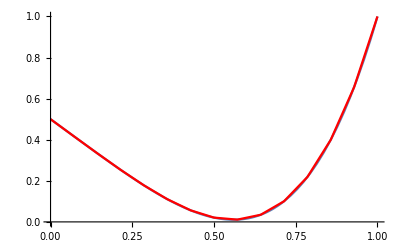

```mathematica
Kglobal=SparseArray[{},{n,n}];
Fglobal=SparseArray[{},{n}];
For[el=1,el<=Length@elems,++el,Kglobal[[elemnumnodes[[el]],elemnumnodes[[el]]]]+=Kloc[elems[[el]]];Fglobal[[elemnumnodes[[el]]]]+=Floc[elems[[el]]]]
Kglobal[[1,1]]+=10^10;
Kglobal[[-1,-1]]+=10^10;
Fglobal[[1]]+=10^10 ul;
Fglobal[[-1]]+=10^10 ur;
usol=LinearSolve[Kglobal,Fglobal];
values=DeleteDuplicates@Partition[Flatten[Table[p1=elems[[i,1]];p2=elems[[i,2]];idx1=elemnumnodes[[i,1]];idx2=elemnumnodes[[i,2]];({p1+#(p2-p1),Subscript[N, 1][#]*usol[[idx1]]+Subscript[N, 2][#]*usol[[idx2]]})&/@Subdivide[0,1,2],{i,Length@elems}]],2];
Show[pl,ListLinePlot[values,PlotStyle->Red]]
```

### Пример 6: базисные функции 2-го порядка

Если мы хотим использовать базисные функции 2-го порядка, на референсном элементе потребуется добавить еще один узел с координатой x=0.5 (для задания параболы нужно три точки). Базисные функции получаем с помощью лагранжевой интерполяции. Например, для N_1 имеем, что N_1(0)=1, N_1(0.5)=N_1(1)=0, следовательно, N_1=((x-0.5)(x-1))/((0-0.5)(0-1))=2(x-1)(x-0.5). Аналогично получаем N_2=4x(1-x) и N_3=2x(x-0.5).

```mathematica
Clear["Global`*"]
f[x_]:=20 x^2
op[f_]:=D[f,x,x]
ul=0.5;
ur=1;
sol=NDSolveValue[{op[y[x]]==f[x],y[0]==ul,y[1]==ur},y[x],x];
pl=Plot[sol,{x,0,1}];
```

Квадратурная формула Гаусса для m точек :

```mathematica
m=3;
poly=Total@Table[Subscript[c, i] x^i,{i,0,2m-1}];
res=Integrate[poly,{x,0,1}];
quad=Total@Table[Subscript[w, j] poly/.x->Subscript[x, j],{j,m}];
unknowns=Flatten@Table[{Subscript[w, j],Subscript[x, j]},{j,m}];
sol=NSolveValues[Table[Coefficient[quad,Subscript[c, i]]==Coefficient[res,Subscript[c, i]],{i,0,2m-1}],unknowns][[1]];
weights=sol[[;;;;2]];
quadpoints=sol[[2;;;;2]];
Quad[f_]:=Dot[weights,(f/.x->#&)/@quadpoints]
```

Задание элементов (n - нечетное, а узлов на элементе теперь 3):

```mathematica
n=9;
nodes=Subdivide[0,1.,n-1];
numnodes=Range[n];
elems=Partition[nodes,3,2]
elemnumnodes=Partition[numnodes,3,2]
```

{{0.,0.125,0.25},{0.25,0.375,0.5},{0.5,0.625,0.75},{0.75,0.875,1.}}

{{1,2,3},{3,4,5},{5,6,7},{7,8,9}}

Задание функций формы и локальных матриц жесткости. Весь код идентичен тому, что для линейных элементов, только теперь три функции формы и локальная матрица и вектор правой части имеют размер 3, а не 2.

```mathematica
Subscript[N, 1][ξ_]:=2(ξ-1)(ξ-0.5)
Subscript[N, 2][ξ_]:=4ξ(1-ξ)
Subscript[N, 3][ξ_]:=2ξ(ξ-0.5)
Subscript[Nd, 1][L2_]:=Evaluate[D[Subscript[N, 1][L2],L2]]
Subscript[Nd, 2][L2_]:=Evaluate[D[Subscript[N, 2][L2],L2]]
Subscript[Nd, 3][L2_]:=Evaluate[D[Subscript[N, 3][L2],L2]]
Kref=Table[Quad[Subscript[Nd, i][x]Subscript[Nd, j][x]],{i,3},{j,3}];
Kloc[points_]:=Kref/(points[[-1]]-points[[1]])
Floc[points_]:=Module[{x1=points[[1]],x3=points[[-1]],J=points[[-1]]-points[[1]]},J Table[Quad[ -Subscript[N, i][x]f[x1+x*J]],{i,3}]]
```

Сборка матрицы, правой части и решение. Код в точности повторяет решение для линейных элементов. Изменяется лишь получение значений для построения графика решения.

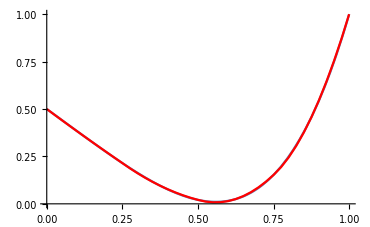

```mathematica
Kglobal=SparseArray[{},{n,n}];
Fglobal=SparseArray[{},{n}];
For[el=1,el<=Length@elems,++el,Kglobal[[elemnumnodes[[el]],elemnumnodes[[el]]]]+=Kloc[elems[[el]]];Fglobal[[elemnumnodes[[el]]]]+=Floc[elems[[el]]]]
Kglobal[[1,1]]+=10^10;
Kglobal[[-1,-1]]+=10^10;
Fglobal[[1]]+=10^10 ul;
Fglobal[[-1]]+=10^10 ur;
usol=LinearSolve[Kglobal,Fglobal];
values=DeleteDuplicates@Partition[Flatten[Table[p1=elems[[i,1]];p2=elems[[i,-1]];idx1=elemnumnodes[[i,1]];idx2=elemnumnodes[[i,2]];
idx3=elemnumnodes[[i,3]];({p1+#(p2-p1),Subscript[N, 1][#]*usol[[idx1]]+Subscript[N, 2][#]*usol[[idx2]]+Subscript[N, 3][#]*usol[[idx3]]})&/@Subdivide[0,1,10],{i,Length@elems}]],2];
Show[pl,ListLinePlot[values,PlotStyle->Red]]
```

### Пример 7: базисные функции произвольного порядка

```mathematica
Clear["Global`*"]
f[x_]:=20 x^2
op[f_]:=D[f,x,x]
ul=0.5;
ur=1;
sol=NDSolveValue[{op[y[x]]==f[x],y[0]==ul,y[1]==ur},y[x],x];
pl=Plot[sol,{x,0,1}];
```

Квадратурная формула Гаусса для m точек :

```mathematica
m=3;
poly=Total@Table[Subscript[c, i] x^i,{i,0,2m-1}];
res=Integrate[poly,{x,0,1}];
quad=Total@Table[Subscript[w, j] poly/.x->Subscript[x, j],{j,m}];
unknowns=Flatten@Table[{Subscript[w, j],Subscript[x, j]},{j,m}];
sol=NSolveValues[Table[Coefficient[quad,Subscript[c, i]]==Coefficient[res,Subscript[c, i]],{i,0,2m-1}],unknowns,Reals][[1]];
weights=sol[[;;;;2]];
quadpoints=sol[[2;;;;2]];
Quad[f_]:=Dot[weights,(f/.x->#&)/@quadpoints]
```

Задание элементов

```mathematica
ORDER=5;
LOCALNODESNUM=ORDER+1;
elemnum=10;
nodes=Subdivide[0,1.,elemnum*ORDER];
nodesnum=Length@nodes;
numnodes=Range[nodesnum];
elems=Partition[nodes,LOCALNODESNUM,LOCALNODESNUM-1];
elemnumnodes=Partition[numnodes,LOCALNODESNUM,LOCALNODESNUM-1];
```

Задание функций формы произвольного порядка (используем лагранжеву интерполяцию для задания функций формы)

```mathematica
refelemnodes=Subdivide[0,1.,ORDER];
For[i=1,i<=LOCALNODESNUM,++i,Subscript[basis, i][x_]:=Evaluate[(∏_(j=1)^(i-1) (x-refelemnodes[[j]])/(refelemnodes[[i]]-refelemnodes[[j]]))*(∏_(j=i+1)^LOCALNODESNUM (x-refelemnodes[[j]])/(refelemnodes[[i]]-refelemnodes[[j]]))];Subscript[Dbasis, i][x_]:=Evaluate@D[Subscript[basis, i][x],x]]
Kref=ParallelTable[Integrate[Subscript[Dbasis, i][x]Subscript[Dbasis, j][x],{x,0,1}],{i,LOCALNODESNUM},{j,LOCALNODESNUM}];
Kloc[points_]:=Kref/(points[[-1]]-points[[1]])
Floc[points_]:=Module[{x1=points[[1]],J=points[[-1]]-points[[1]]},J Table[Quad[ -Subscript[basis, i][x]f[x1+x*J]],{i,LOCALNODESNUM}]]
```

Решение

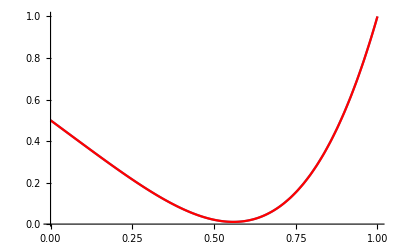

```mathematica
Kglobal=SparseArray[{},{nodesnum,nodesnum}];
Fglobal=SparseArray[{},{nodesnum}];
For[el=1,el<=Length@elems,++el,Kglobal[[elemnumnodes[[el]],elemnumnodes[[el]]]]+=Kloc[elems[[el]]];Fglobal[[elemnumnodes[[el]]]]+=Floc[elems[[el]]]]
Kglobal[[1,1]]+=10^10;
Kglobal[[-1,-1]]+=10^10;
Fglobal[[1]]+=10^10 ul;
Fglobal[[-1]]+=10^10 ur;
usol=LinearSolve[Kglobal,Fglobal];
values=DeleteDuplicates@Partition[Flatten[Table[p1=elems[[i,1]];p2=elems[[i,-1]];{p1+#(p2-p1),Dot[Table[Subscript[basis, i][#],{i,LOCALNODESNUM}],usol[[elemnumnodes[[i]]]]]}&/@Subdivide[0,1,20],{i,Length@elems}]],2];
Show[pl,ListLinePlot[values,PlotStyle->Red],PlotRange->All]
```

## МКЭ 2d

### Пример 8: линейные функции формы на треугольнике, без барицентрических координат

(R,v)=(∇^2 u-f,v)=∫_V (∇^2 u)vⅆV-∫_V fvⅆV=//Используем формулу ∇.(∇u*v)=∇^2 u*v+(∇u).(∇v)//=
=∫_V ∇.(∇u*v)ⅆV-∫_V (∇u).(∇v)ⅆV-∫_V fvⅆV=∫_S (∂u)/(∂n)*vⅆS-∫_V (∇u).(∇v)ⅆV-∫_V fvⅆV=
//αu+β(∂u)/(∂n)=γ,(∂u)/(∂n)=γ/β-α/β u//=∫_S (γ/β-α/β u)vⅆS-∫_V (∇u).(∇v)ⅆV-∫_V fvⅆV=0.

Уравнение ∇^2 u=f, (x,y)∈[0;1]x[0;1]
Граничное условие u=u0

```mathematica
f[x_,y_]:=x^2+y^2-(x+y)
u0=0;
sol=NDSolveValue[{Laplacian[u[x,y],{x,y}]==f[x,y],DirichletCondition[u[x,y]==u0,True]},u[x,y],{x,0,1},{y,0,1}];
pl=Plot3D[sol,{x,0,1},{y,0,1},PlotStyle->{Cyan,Opacity[0.5]}]
```

-Graphics3D-

Область :

```mathematica
reg=Rectangle[{0,0},{1,1}];
```

Максимальная площадь треугольника в сетке :

```mathematica
Smax=0.01;
```

Сетка :

```mathematica
Needs["NDSolve`FEM`"];
mesh=ToElementMesh[reg,MaxCellMeasure->Smax,"MeshOrder"->1,"MeshElementType"->"TriangleElement","NodeReordering"->True];
```

Та же сетка, но если она meshregion, с ней удобнее работать :

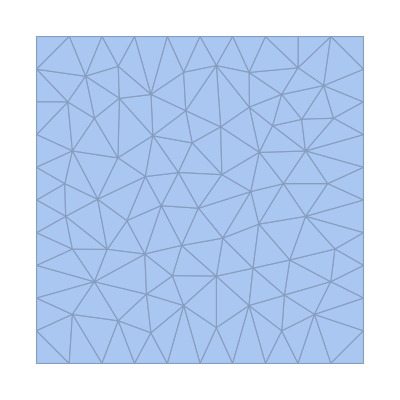

```mathematica
mesh1=MeshRegion[mesh]
```

Координаты узлов :

```mathematica
nodescoordinates=MeshCoordinates[mesh1];
```

Количество узлов и элементов :

```mathematica
nodNum=MeshCellCount[mesh1,0]
elNum=MeshCellCount[mesh1,2]
```

100

158

Номера узлов для каждого элемента :

```mathematica
elementnodesnumbers=MeshCells[mesh1,2][[;;,1]];
elementnodesnumbers[[1]]
```

{48,62,47}

Координаты узлов для каждого элемента :

```mathematica
elementnodescoordinates=nodescoordinates[[#]]&/@elementnodesnumbers;
```

Граничные ребра (с номерами узлов) и номера всех узлов на границе:

```mathematica
boundaryedges=mesh["BoundaryElements"][[1,1]];
boundarynodes=DeleteDuplicates@Flatten@boundaryedges
```

{51,50,52,53,86,25,29,27,43,31,34,32,33,55,35,58,90,56,1,62,19,47,3,83,16,69,7,68,10,66,67,74,72,78,64,91,5,13,9,8}

Нормали к граничным ребрам :

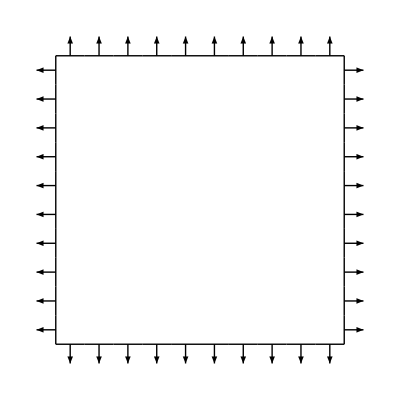

```mathematica
bmesh=ToBoundaryMesh[mesh1];
mean=Mean/@GetElementCoordinates[bmesh["Coordinates"],#]&/@ElementIncidents[bmesh["BoundaryElements"]];
tangents=(Differences[#]&/@(nodescoordinates[[#]]&/@(Sort/@boundaryedges)))[[;;,1]];
normals=#/Norm[#]&/@(-{#[[1,2]],-#[[1,1]]}&/@(Differences[#]&/@(nodescoordinates[[#]]&/@boundaryedges)));
Show[bmesh["Wireframe"],Graphics[MapThread[Arrow[{#1,#2}]&,{Join@@mean,Join@@({normals}/15+mean)}]]]
```

Функции формы на произвольном элементе :

```mathematica
Subscript[NN, 1][ξ_,η_]:=1-ξ-η
Subscript[NN, 2][ξ_,η_]:=ξ
Subscript[NN, 3][ξ_,η_]:=η
Fx[{{x1_,y1_},{x2_,y2_},{x3_,y3_}},ξ_,η_]:=(x2-x1)ξ + (x3-x1)η + x1
Fy[{{x1_,y1_},{x2_,y2_},{x3_,y3_}},ξ_,η_]:= (y2-y1)ξ + (y3-y1)η + y1
```

Локальные матрица жесткости и правая часть :

```mathematica
a=(-y1+y3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
b=(x1-x3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
d=(y1-y2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
e=(-x1+x2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
```

```mathematica
J={{a,b},{d,e}};
```

```mathematica
ktemp[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=Evaluate@Table[Integrate[Transpose[J].Grad[Subscript[NN, i][ξ,η],{ξ,η}].Transpose[J].Grad[Subscript[NN, j][ξ,η],{ξ,η}],{ξ,η}∈Triangle[{{0,0},{1,0},{0,1}}]],{i,3},{j,3}];
```

```mathematica
Kloc[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=Evaluate[2*Area[Triangle[{{x1,y1},{x2,y2},{x3,y3}}]]*ktemp[{{x1,y1},{x2,y2},{x3,y3}}]]
Floc[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=2*Area[Triangle[{{x1,y1},{x2,y2},{x3,y3}}]]*Table[FullSimplify@NIntegrate[-Subscript[NN, i][ξ,η]f[Fx[{{x1,y1},{x2,y2},{x3,y3}},ξ,η],Fy[{{x1,y1},{x2,y2},{x3,y3}},ξ,η]],{ξ,η}∈Triangle[{{0,0},{1,0},{0,1}}]],{i,3}]
```

Сборка матрицы и правой части :

```mathematica
Kglobal=ConstantArray[0,{nodNum,nodNum}];
For[i=1,i<=elNum,i++,Kglobal[[elementnodesnumbers[[i]],elementnodesnumbers[[i]]]]+=Kloc[elementnodescoordinates[[i]]]]
Fglobal=ConstantArray[0,{nodNum}]; 
For[i=1,i<=elNum,i++,Fglobal[[elementnodesnumbers[[i]]]]+=Floc[elementnodescoordinates[[i]]]]
```

Задание граничного условия Дирихле :

```mathematica
For[i=1,i<=Length@boundarynodes,++i,Kglobal[[boundarynodes[[i]],boundarynodes[[i]]]]+=10^20;Fglobal[[boundarynodes[[i]]]]+=10^20 u0]
```

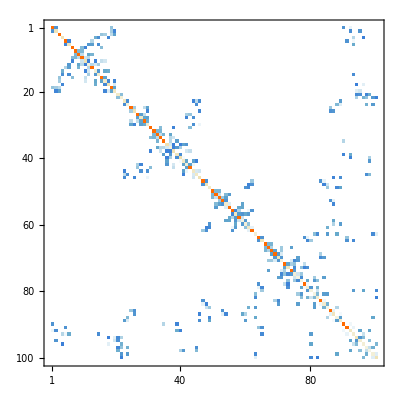

```mathematica
MatrixPlot[Kglobal]
```

Решение и построение графика :

```mathematica
usol=Quiet@LinearSolve[Kglobal,Fglobal];
plotsol=Table[Flatten[{nodescoordinates[[i]],usol[[i]]}],{i,nodNum}];
Show[pl,ListPlot3D[plotsol,PlotStyle->Opacity[0.5]]]
```

-Graphics3D-

```mathematica
Ψ[x_,y_]:=1/2 x*(1-x)*y*(1-y)
```

```mathematica
Laplacian[Ψ[x,y],{x,y}]
```

-((1-x) x)-(1-y) y

```mathematica
exactSol =Table[Ψ[nodescoordinates[[i,1]],nodescoordinates[[i,2]]],{i, Length@nodescoordinates}];
```

```mathematica
Max[Abs[usol-exactSol]]/Max[Abs[exactSol]]
```

0.0141819

```mathematica
Solve[{aa Subscript[x, 1]+b Subscript[y, 1]+c ==0, d Subscript[x, 1]+e Subscript[y, 1]+f ==0, a Subscript[x, 2]+b Subscript[y, 2]+c ==1, d Subscript[x, 2]+e Subscript[y, 2]+f ==0, a Subscript[x, 3]+b Subscript[y, 3]+c ==0, d Subscript[x, 3]+e Subscript[y, 3]+f ==1}, {aa_,b, c, d, e, f}]
```

```mathematica
Solve[{a Subscript[x, 1]+b Subscript[y, 1]+c ==0, a Subscript[x, 2]+b Subscript[y, 2]+c ==1, a Subscript[x, 3]+b Subscript[y, 3]+c ==0}, {a,b,c}]//FullSimplify
```

Solve::ivar: (-y1+y3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)) is not a valid variable.

Solve[{(c (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(-y1+y3) x_1+(x1-x3) y_1)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))==0,c+((-y1+y3) x_2+(x1-x3) y_2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))==1,(c (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(-y1+y3) x_3+(x1-x3) y_3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))==0},{(y1-y3)/(x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3),(x1-x3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)),c}]

```mathematica
Solve[{d Subscript[x, 1]+e Subscript[y, 1]+f ==0, d Subscript[x, 2]+e Subscript[y, 2]+f ==0, d Subscript[x, 3]+e Subscript[y, 3]+f ==1}, {d,e,f}]//FullSimplify
```

Solve::ivar: (y1-y2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)) is not a valid variable.

Solve[{(f (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(y1-y2) x_1+(-x1+x2) y_1)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))==0,(f (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(y1-y2) x_2+(-x1+x2) y_2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))==0,f+((y1-y2) x_3+(-x1+x2) y_3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))==1},{(y1-y2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)),(x1-x2)/(x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3),f}]

```mathematica
Det[{{1,1,1},{x1,x2,x3},{y1,y2,y3}}]//FullSimplify
```

x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)

```mathematica
Area[Triangle[{{x1,y1},{x2,y2},{x3,y3}}]]
```

1/2 Abs[-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3]

```mathematica
(-Subscript[y, 1]+Subscript[y, 3])/(Subscript[x, 3] (Subscript[y, 1]-Subscript[y, 2])+Subscript[x, 1] (Subscript[y, 2]-Subscript[y, 3])+Subscript[x, 2] (-Subscript[y, 1]+Subscript[y, 3]))*(-Subscript[x, 1]+Subscript[x, 2])/(Subscript[x, 3] (Subscript[y, 1]-Subscript[y, 2])+Subscript[x, 1] (Subscript[y, 2]-Subscript[y, 3])+Subscript[x, 2] (-Subscript[y, 1]+Subscript[y, 3]))-(Subscript[x, 1]-Subscript[x, 3])/(Subscript[x, 3] (Subscript[y, 1]-Subscript[y, 2])+Subscript[x, 1] (Subscript[y, 2]-Subscript[y, 3])+Subscript[x, 2] (-Subscript[y, 1]+Subscript[y, 3]))*(Subscript[y, 1]-Subscript[y, 2])/(Subscript[x, 3] (Subscript[y, 1]-Subscript[y, 2])+Subscript[x, 1] (Subscript[y, 2]-Subscript[y, 3])+Subscript[x, 2] (-Subscript[y, 1]+Subscript[y, 3]))//FullSimplify
```

1/(x_3 (y_1-y_2)+x_1 (y_2-y_3)+x_2 (-y_1+y_3))

```mathematica
a=(-y1+y3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
b=(x1-x3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
d=(y1-y2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
e=(-x1+x2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
```

```mathematica
J={{a,b},{d,e}};
```